# ARM -10R with ergonomic constraint- weight to be set

## Alessia Biondi June 2020

Brief description of notebook purpose

What is done inside this notebook:
first, it is implemented the reconstruction of an ideal trajectory from data provided by IMU sensors placed on subjects’arm during the execution of a specific task (only using the end effector position, here hand position). 
Then, it is defined a functional cost (J) in order to encourage the most ergonomic arm’s movement.
After that, inverse Kinematic is implemented: it is imposed as trajectory to be followed the one obtained from data about hand movements. Here, CLIK is a redoundant problem because of the redundant degrees of freedom of a 10R arm: these redundancies are used to impose ergonomic constraints by functional cost’s minimization (J, defined above).
Finally, joints’ angles obtained as CLIK result (10 angles values) will be the ones that allow the execution of the task by minimizing J, so trying to follow the more ergonomic way to execute it.

## General setting

## Loading Data and Parameters

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
<<ScrewCalculusPro`
<<OdeSolve`
```

Current trial execution: “H01 T07 L1”
It is about the first healthy (H) subject that executes the task number 7 (T07) using his left arm (L) (first of three trials)

### Data Load

```mathematica
(* Data are imported from .csv files generated using Matlab function "writematrix" on data structures.
  Inside handr/handl are loaded position and orientation of the hand during all task execution: these values provide us the trajectory to be followed during inverse kinematics execution.
Inside parr/parl are loaded all parameters needed in order to build the arm of each subject using real size. *)
```

```mathematica
Handr = Import["H01_T07_L1_hand_R.csv"];
```

```mathematica
Handl = Import["H01_T07_L1_hand_L.csv"];
```

```mathematica
Handvr = Import["H01_T07_L1_hand_vR.csv"];
```

```mathematica
Handvl = Import["H01_T07_L1_hand_vL.csv"];
```

```mathematica
parr = Import["H01_T07_L1_par_R.csv"]; parr//TableForm
```

L5_pos_x | L5_pos_y | L5_pos_z | L5_shoulder_dist | depth_shoulder | theta_shoulder | upperarm_length | forearm_length
-0.1964 | 0.012548 | 0.92348 | 0.39413 | 0.14293 | 0.3998 | 0.31801 | 0.26032

```mathematica
parl = Import["H01_T07_L1_par_L.csv"]; parl//TableForm
```

L5_pos_x | L5_pos_y | L5_pos_z | L5_shoulder_dist | depth_shoulder | theta_shoulder | upperarm_length | forearm_length
-0.1964 | 0.012548 | 0.92348 | 0.39403 | 0.11261 | 0.46639 | 0.31801 | 0.26032

Initial Config calculated in Matlab:

```mathematica
q0 = Import["H01_T07_L1_q0.csv"]; q0//TableForm
```

0.200939 | -0.163933 | -0.137383 | -1.5132 | -0.646139 | 0.469654 | 0.0440366 | 0.468694 | 0.033179 | 0.29317
0.347153 | -0.236104 | -0.203084 | -1.53884 | -0.577991 | 0.423292 | -0.0711882 | 0.423276 | -0.172628 | 0.061222

```mathematica
q0r = q0[[1]];
```

```mathematica
q0l = q0[[2]];
```

```mathematica
samplerate = 60;
```

```mathematica
t0 = 1/samplerate ;
```

```mathematica
tend = (Length [Handr]-1)/samplerate;
```

### Parameters for both arm

#### Graphic Plot Par

```mathematica
xmin3d = -1.5;
xmax3d = 1.5;
ymin3d = -1.5;
ymax3d = 1.5;
zmin3d = 0;
zmax3d = 1.5;
```

#### Joint Angles Range

```mathematica
nangoliH=4;
RANGEq1=Pi/2;
RANGEq2=Pi/2;
RANGEq3=(15/180 *Pi);
RANGEq5=Pi/2 ;
```

```mathematica
(*
RANGEq4=(15/180 *Pi);
RANGEq5=(15/180 *Pi);
RANGEq6=(15/180 *Pi);
RANGEq7=(15/180 *Pi);
RANGEq8=(15/180 *Pi);
RANGEq9=(15/180 *Pi);
RANGEq10=(15/180 *Pi); 
*)
```

#### Gains for CLIK

```mathematica
weights  = {100,100,100,50,50,40,10,1,1,1};
```

```mathematica
W = weights * IdentityMatrix[10]; W//MatrixForm
```

(100 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 100 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 100 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 20 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 20 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 20 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

Proportional Gain parameters to the close loop inverse Kinematics

```mathematica
ko = 20;
```

```mathematica
kp = 50;
```

## General Functions

```mathematica
xAxis =  Table[i, {i, Length[Handl]-1}];
```

```mathematica
(* Plot of a_, xAxis represents number of samples. Corresponding time value = xAsis /samplerate *)
```

```mathematica
Draw[a_] := Manipulate[
b = Transpose [a];
ListLinePlot[
Transpose[{xAxis, (b)}], 
ImageSize -> 1100*Scala, AspectRatio -> 0.25/Scala, PlotRange -> {{xx, xx + Δxx}, All}], 
{{Scala, 1}, 0.1, 4}, {{xx, 0}, 0, Max[xAxis]}, {{Δxx, Max[xAxis]*1.05}, 0, Max[xAxis]*1.05} ]
```

```mathematica
(* Plot of a_ splitted along every single axis of the frame it is referred to *)
```

```mathematica
Draw3[a_] := Manipulate[
b = Transpose [a];
ListLinePlot[
{Transpose[{xAxis, (b[[1]])}], 
Transpose[{xAxis, (b[[2]])}],
Transpose[{xAxis, (b[[3]])}]},
ImageSize -> 1100*Scala, AspectRatio -> 0.25/Scala, PlotRange -> {{xx, xx + Δxx}, All}], 
{{Scala, 1}, 0.1, 4}, {{xx, 0}, 0, Max[xAxis]}, {{Δxx, Max[xAxis]*1.05}, 0, Max[xAxis]*1.05} ]
```

```mathematica
InterpLin[a_,b_,t_]:= If[t>1, ErrorBox,a+ (b-a) * t];
```

## Right Arm

## Hand trajectory definition

We have DT data, 60 sample each second, so we have to interpolate between samples because a CT trajectory is needed inside inverse kinematic algorithm.

#### Load Data

```mathematica
(* skip first row: data description *)
```

```mathematica
handr = Drop[Handr,1];
```

```mathematica
handvr = Drop[Handvr,1];
```

```mathematica
(* pos and quat extraction *)
```

```mathematica
dataposr = Transpose[Transpose[handr][[1;;3]]];
```

```mathematica
dataquatr = Transpose[Transpose[handr][[4;;7]]];
```

```mathematica
datavelr = Transpose[Transpose[handvr][[1;;3]]];
```

```mathematica
dataangvelr = Transpose[Transpose[handvr][[4;;6]]];
```

#### Orientation

```mathematica
(* quat interpolation using slerp *)
```

```mathematica
quatr[time_]=  
If[time≥tend, 
	time2 = tend-0.001;
	Re[Slerp[
		i=Floor[time2*samplerate];
		t=time2* samplerate -i;
		dataquatr[[i]],
		dataquatr[[ i+1]],
		t
	]]
,
	Re[Slerp[
		i=Floor[time*samplerate];
		t=time * samplerate -i;
		dataquatr[[i]],
		dataquatr[[ i+1]],
		t
	]]
]
```

If[time≥3,time2=tend-0.001;Re[Slerp[i=Floor[time2 samplerate];t=time2 samplerate-i;dataquatr⟦i⟧,dataquatr⟦i+1⟧,t]],Re[Slerp[i=Floor[time samplerate];t=time samplerate-i;dataquatr⟦i⟧,dataquatr⟦i+1⟧,t]]]

#### Position

```mathematica
(* position linear interpolation *)
```

```mathematica
posr[time_]=  
If[time≥tend, 
	time2 = tend-0.001;
	InterpLin[
		i=Floor[time2*samplerate];
		t=time2* samplerate -i;
		dataposr[[i]],
		dataposr[[ i+1]],
		t
	]
,
	InterpLin[
		i=Floor[time*samplerate];
		t=time * samplerate -i;
		dataposr[[i]],
		dataposr[[ i+1]],
		t
	]
]
```

If[time≥3,time2=tend-0.001;InterpLin[i=Floor[time2 samplerate];t=time2 samplerate-i;dataposr⟦i⟧,dataposr⟦i+1⟧,t],InterpLin[i=Floor[time samplerate];t=time samplerate-i;dataposr⟦i⟧,dataposr⟦i+1⟧,t]]

#### Homogeneous Transform

```mathematica
(* RotX[Pi/2]: to reorient data from local Xsens frame (IMU frame) to global frame  *)
```

```mathematica
REEr[time_] :=QuatToMat[quatr[time]].RotX[Pi/2];
```

```mathematica
TEEr[time_] := RPToHomogeneous[REEr[time],posr[time]];
```

#### Angular velocity

```mathematica
(* angular velocity linear interpolation *)
```

```mathematica
angvelr[time_]=  
If[time≥tend, 
	time2 = tend-0.001;
	InterpLin[
		i=Floor[time2*samplerate];
		t=time2* samplerate -i;
		dataangvelr[[i]],
		dataangvelr[[ i+1]],
		t
	]
,
	InterpLin[
		i=Floor[time*samplerate];
		t=time * samplerate -i;
		dataangvelr[[i]],
		dataangvelr[[ i+1]],
		t
	]
]
```

If[time≥3,time2=tend-0.001;InterpLin[i=Floor[time2 samplerate];t=time2 samplerate-i;dataangvelr⟦i⟧,dataangvelr⟦i+1⟧,t],InterpLin[i=Floor[time samplerate];t=time samplerate-i;dataangvelr⟦i⟧,dataangvelr⟦i+1⟧,t]]

#### Linear velocity

```mathematica
(* linear velocity linear interpolation *)
```

```mathematica
velr[time_]=  
If[time≥tend, 
	time2 = tend-0.001;
	InterpLin[
		i=Floor[time2*samplerate];
		t=time2* samplerate -i;
		datavelr[[i]],
		datavelr[[ i+1]],
		t
	]
,
	InterpLin[
		i=Floor[time*samplerate];
		t=time * samplerate -i;
		datavelr[[i]],
		datavelr[[ i+1]],
		t
	]
]
```

If[time≥3,time2=tend-0.001;InterpLin[i=Floor[time2 samplerate];t=time2 samplerate-i;datavelr⟦i⟧,datavelr⟦i+1⟧,t],InterpLin[i=Floor[time samplerate];t=time samplerate-i;datavelr⟦i⟧,datavelr⟦i+1⟧,t]]

## 10R construction Denavit Hartenberg

### Parameters

```mathematica
(* Parameters assignment using loaded data *)
```

```mathematica
L5Rot = RotX[-Pi/2];
```

```mathematica
L5Pos = {parl[[2]][[1]] , parl[[2]][[2]],parl[[2]][[3]]};
```

```mathematica
Tg0 = RPToHomogeneous[L5Rot, L5Pos];
```

```mathematica
Tg = RPToHomogeneous[IdentityMatrix[3], L5Pos];
```

```mathematica
θr=parr[[2]][[6]];
```

```mathematica
a3r=parr[[2]][[4]];
```

```mathematica
d3r=parr[[2]][[5]];
```

```mathematica
d6r=-parr[[2]][[7]];
```

```mathematica
d8r=-parr[[2]][[8]];
```

```mathematica
d10r=0;
```

### Denavit Hartenberg Table and EE transform

Note: “g” frame is the provided global frame in which the data are expressed.

```mathematica
θ3r = -Pi/2 - θr;
α4r = Pi/2 + θr;
```

```mathematica
(* Denavit Hartenberg Table for right arm *)
```

```mathematica
(* DH order is: a, alpha, d, theta *)
```

```mathematica
T01r[q1_]=DH[{0,+Pi/2,0,q1,"R"}];
```

```mathematica
T12r[q2_]=DH[{0,-Pi/2,0,q2 + Pi/2,"R"}];
```

```mathematica
T23r[q3_]=DH[{a3r,Pi/2,d3r,q3 + θ3r,"R"}];
```

```mathematica
T34r[q4_]=DH[{0,α4r,0,q4 + Pi/2,"R"}];
```

```mathematica
T45r[q5_]=DH[{0,-Pi/2,0,q5 - Pi/2,"R"}];
```

```mathematica
T56r[q6_]=DH[{0,Pi/2,d6r,q6,"R"}];
```

```mathematica
T67r[q7_]=DH[{0,Pi/2,0,q7 + Pi,"R"}];
```

```mathematica
T78r[q8_]=DH[{0,-Pi/2,d8r,q8,"R"}];
```

```mathematica
T89r[q9_]=DH[{0,Pi/2,0,q9 + Pi/2,"R"}];
```

```mathematica
T910r[q10_]=DH[{0,Pi/2,d10r,q10 + Pi/2,"R"}];
```

```mathematica
(* EE transform: right hand *)
```

```mathematica
TgEEr[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}]=Tg0.T01r[q1].T12r[q2].T23r[q3].T34r[q4].T45r[q5].T56r[q6].T67r[q7].T78r[q8].T89r[q9].T910r[q10];
```

```mathematica
TgEErInv[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = RigidInverse[TgEEr[{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10}]];
```

```mathematica
posEEr[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}]=RigidPosition[TgEEr[{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10}]];
```

```mathematica
orEErInv[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}]=RigidOrientation[TgEErInv[{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10}]];
```

### Jacobian

#### DH table

```mathematica
DHtabler[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] ={
{0,+Pi/2,0,q1,"R"},
{0,-Pi/2,0,q2 + Pi/2,"R"},
{a3r,Pi/2,d3r,q3 + θ3r,"R"},
{0,α4r,0,q4 + Pi/2,"R"},
{0,-Pi/2,0,q5 - Pi/2,"R"},
{0,Pi/2,d6r,q6,"R"},
{0,Pi/2,0,q7 + Pi,"R"},
{0,-Pi/2,d8r,q8,"R"},
{0,Pi/2,0,q9 + Pi/2,"R"},
{0,Pi/2,d10r,q10 + Pi/2,"R"}
};
```

#### Jacobian

DHJacobBase::usage = "DHJacobBase[DHtable, Tb0] computes the DH spatial Jacobian for the supplied DH table DHtable, w.r.t. a base frame Sb (both origin and orientation are considered) \nwhere the displacement from Sb to S0 is expressed by the homogeneous matrix Tb0."

```mathematica
(* Definition of geometric arm Jacobian from DH parametrization *)
```

```mathematica
Jacr[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = DHJacobBase[DHtabler[{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10}], Tg0];
```

```mathematica
(* sanity check- we obtain linear and angular velocity of hand wrt our global frame *)
```

```mathematica
Jacr[{0,0,0,0,0,0,0,0,0,0}].{0,0,0,0,0,0,0,0,0,0};
```

### Homogeneous Transform

```mathematica
(* Tgir = homogeneous transformation from global frame to "i" frame *)
```

```mathematica
Tg1r[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = Tg0.T01r[q1];
```

```mathematica
Tg2r[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = Tg0.T01r[q1].T12r[q2];
```

```mathematica
Tg3r[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = Tg0.T01r[q1].T12r[q2].T23r[q3];
```

```mathematica
Tg4r[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = Tg0.T01r[q1].T12r[q2].T23r[q3].T34r[q4];
```

```mathematica
Tg5r[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = Tg0.T01r[q1].T12r[q2].T23r[q3].T34r[q4].T45r[q5];
```

```mathematica
Tg6r[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = Tg0.T01r[q1].T12r[q2].T23r[q3].T34r[q4].T45r[q5].T56r[q6];
```

```mathematica
Tg7r[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = Tg0.T01r[q1].T12r[q2].T23r[q3].T34r[q4].T45r[q5].T56r[q6].T67r[q7];
```

```mathematica
Tg8r[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = Tg0.T01r[q1].T12r[q2].T23r[q3].T34r[q4].T45r[q5].T56r[q6].T67r[q7].T78r[q8];
```

```mathematica
Tg9r[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = Tg0.T01r[q1].T12r[q2].T23r[q3].T34r[q4].T45r[q5].T56r[q6].T67r[q7].T78r[q8].T89r[q9];
```

```mathematica
Tg10r[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = Tg0.T01r[q1].T12r[q2].T23r[q3].T34r[q4].T45r[q5].T56r[q6].T67r[q7].T78r[q8].T89r[q9].T910r[q10];
```

## Inverse Kinematic : CLIK with constrains

### Functional definition

```mathematica
(* Weight matrix inside functional def *)
```

```mathematica
Jwr[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] := Inverse[W].Transpose[Jacr[{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10}]].Inverse[Jacr[{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10}].Inverse[W].Transpose[Jacr[{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10}]]];
```

### Position and orientation error of the end-effector

```mathematica
(* Position error = difference between the desired position of the EE over the ideal trajectory to be followed and the position of the EE over the real trajectory that it perform depending on joint angles *)
```

```mathematica
(* posr is the desired position of the EE, posEEr is the position of EE coming from direct kinematic solution using joint angles *)
```

```mathematica
ePr[time_,{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}]:=(posr[time]-posEEr[{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10}]);
```

```mathematica
(* Orientation error is computed using quaternions by imposing that the product  between the quaternion describing the desired orientation and the quaternion that describe the inverse of the actual orientation of the EE (depending on joint angles) is equal to the Identity matrix *)
```

```mathematica
(* REEr is the desired orientation of the EE, orEEr is the orientation of EE coming from direct kinematic solution using joint angles *)
```

```mathematica
eOr[time_,{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}]:=QuatVectPart[(REEr[time].orEErInv[{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10}])];
```

### Gain matrices of the trajectory tracking law and qdot

```mathematica
(* Proportional Gain constant defined inside Loading Data and Parameters-Parameters for both arm-Gains for CLIK *)
```

```mathematica
KP=kp IdentityMatrix[3];
```

```mathematica
KO=ko IdentityMatrix[3];
```

Control law: OverDot[q̲]=J_w^R((v̲)_des+K_P(e̲)_P
(ω̲)_des+K_O(e̲)_O)

```mathematica
qpr[time_,{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}]:=Jwr[{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10}].(Join[velr[time]+KP.ePr[time,{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10}],angvelr[time]+KO.eOr[time,{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10}]]);
```

```mathematica
qpr[2,{0,0,0,0,0,0,0,0,0,0}]
```

{-51.174,-38.5884,-14.191,-90.0371,-3.36186,0.515777,-6.40267,20.6311,21.161,21.3901}

```mathematica
(* velr = linear velocity from data (real values)
angvelr = linear velocity from data (real values)*)
```

### Integration of the kinematics

Time horizon

```mathematica
t0=1/samplerate;
```

#### Solution

```mathematica
(* Differential equation resolution , with given initial condition *)
```

```mathematica
solr=NDSolve[Join[{Equal[D[q[time],time],qpr[time,q[time]]],Equal[q[t0],q0r]}],q,{time,t0+ 0.01,tend- 0.01}];
```

```mathematica
qsolr[time_]=Evaluate[q[time]/.solr[[1]]];
```

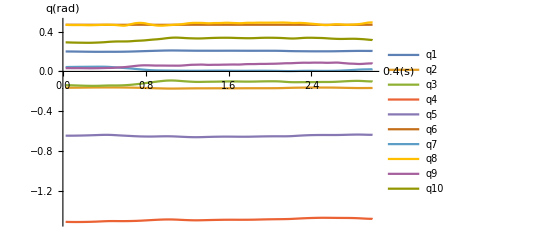

```mathematica
Plot[{qsolr[time][[1]], qsolr[time][[2]], qsolr[time][[3]], qsolr[time][[4]], qsolr[time][[5]], qsolr[time][[6]],qsolr[time][[7]], qsolr[time][[8]], qsolr[time][[9]], qsolr[time][[10]]}, {time,t0+ 0.01,tend- 0.01}, AxesLabel -> {t[s], q[rad]}, PlotLegends -> {"q1", "q2", "q3", "q4", "q5", "q6", "q7", "q8", "q9", "q10"}]
```

#### Hand error

```mathematica
ErrPOSsolr[time_] = ePr[time, qsolr[time]];
```

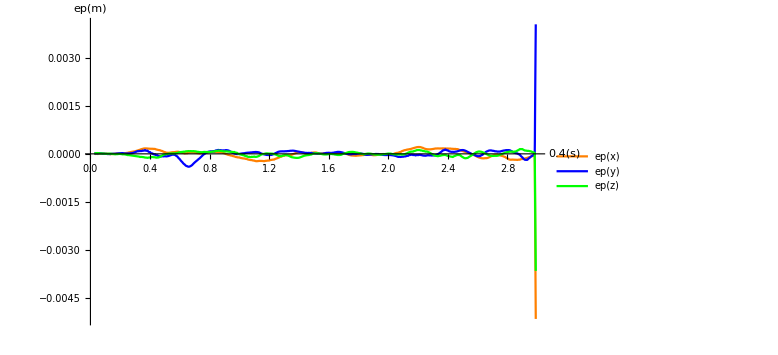

```mathematica
Plot[{ErrPOSsolr[time][[1]], ErrPOSsolr[time][[2]], ErrPOSsolr[time][[3]]}, {time, t0+0.01, tend-0.01}, PlotStyle -> {Orange, Blue, Green}, ImageSize -> Large, PlotRange -> All, TargetUnits -> { "Seconds", "Meters"}, AxesLabel -> {t[s], ep[m]}, PlotLegends -> {"ep(x)", "ep(y)", "ep(z)"}]
```

```mathematica
ErrORsolr[time_] = eOr[time, qsolr[t]];
```

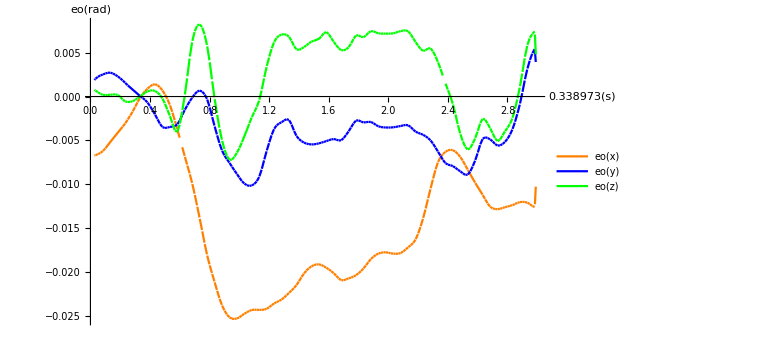

```mathematica
Plot[{ErrORsolr[time][[1]], ErrORsolr[time][[2]], ErrORsolr[time][[3]]}, {time, t0+0.01, tend-0.01}, PlotStyle -> {Orange, Blue, Green}, ImageSize -> Large, PlotRange -> All, AxesLabel -> {t[s], eo[rad]}, PlotLegends -> {"eo(x)", "eo(y)", "eo(z)"}]
```

## 3D elements

### Plane

```mathematica
(* grid representing floor *)
```

```mathematica
passo = (xmax3d - xmin3d)/4; (* grid cell size, scaled in order to always hav ethe same number of cells *)
```

```mathematica
pianopts = Table[{x, y, 0}, {x, xmin3d, xmax3d, passo}, {y, ymin3d, ymax3d, passo}];
```

```mathematica
(* graphic representation of the defined grid *)
```

```mathematica
piano = Map[Graphics3D, {Map[{LightGray, Line[#]} &, pianopts], Map[{Gray, Line[#]} &, Transpose[pianopts]]}];
```

### Base

```mathematica
(* sphere representing L5 *)
```

```mathematica
rbase = 0.08;
```

```mathematica
base = Graphics3D[{Gray, Opacity[0.9], Specularity[White, 30], Sphere[L5Pos, rbase]}];
```

### Robot

```mathematica
(* Position and orientation of each joints' node of the ARM *)
```

#### Points evaluation

```mathematica
dg1r[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = RigidPosition[Tg1r[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]];
```

```mathematica
dg2r[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = RigidPosition[Tg2r[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]];
```

```mathematica
dg3r[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = RigidPosition[Tg3r[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]];
```

```mathematica
dg4r[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = RigidPosition[Tg4r[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]];
```

```mathematica
dg5r[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = RigidPosition[Tg5r[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]];
```

```mathematica
dg6r[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = RigidPosition[Tg6r[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]];
```

```mathematica
dg7r[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = RigidPosition[Tg7r[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]];
```

```mathematica
dg8r[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = RigidPosition[Tg8r[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]];
```

```mathematica
dg9r[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = RigidPosition[Tg9r[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]];
```

```mathematica
dg10r[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = RigidPosition[Tg10r[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]];
```

```mathematica
giuntir[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = {
   L5Pos,
   dg1r[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}],
   dg2r[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}],
   dg3r[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}],
   dg4r[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}],
   dg5r[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}],
   dg6r[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}],
   dg7r[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}],
   dg8r[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}],
   dg9r[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}],
   dg10r[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]   
};
```

#### Tube

```mathematica
(* Tube insertion between two consecutive joints in order to represent the link *)
```

```mathematica
rrobot = 0.05; (* human like arm dimension *)
```

```mathematica
robotr[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = Graphics3D[{Cyan, Opacity[0.6], Specularity[White, 60], CapForm["Butt"], Tube[{giuntir[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]}, rrobot]}];
```

### Reference frames

```mathematica
(* three different reference frames will be plotted: Base, Right end-effector and left end-effector *)
```

```mathematica
(* Reference frame representation, drawed using (0,0,0) as origin and (x, y, z) as axis directions. *)
```

```mathematica
lf = 0.25; (* reference frame axis length *)
e1d = {lf, 0, 0, 1}; e2d = {0, lf, 0, 1}; e3d = {0, 0, lf, 1}; Orig = {0, 0, 0, 1};
Ox = Transpose[Drop[#.Transpose[{Orig, e1d}], -1]] &;
Oy = Transpose[Drop[#.Transpose[{Orig, e2d}], -1]] &;
Oz = Transpose[Drop[#.Transpose[{Orig, e3d}], -1]] &;
Otot = {Ox[#], Oy[#], Oz[#]} &;
```

```mathematica
(* "Reference frame" representation draws over: base, right end-effector and left end-effector *)
```

```mathematica
rifg = Graphics3D[{Red, Thick, Line /@ Otot@Tg}];
```

```mathematica
rifEEr[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] :=  Graphics3D[{
{Red, Thick, Line[Ox@TgEEr[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]]},
{Green, Thick, Line[Oy@TgEEr[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]]},
{Blue, Thick, Line[Oz@TgEEr[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]]}
}];
```

```mathematica
(* x: red, y: green, z: blue *)
```

```mathematica
riftimeEEr[time_] := Graphics3D[{
{Red, Thick, Line [ Ox@TEEr[time]]},
{Green, Thick, Line [ Oy@TEEr[time]]},
{Blue, Thick, Line [ Oz@TEEr[time]]}}];
```

### Assiemi

```mathematica
(* Put all defined elements together *)
```

```mathematica
assiemer[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = {base,rifg, rifEEr[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}], piano, robotr[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]};
```

## Animation and 3D Plots

```mathematica
Manipulate[
Show[
riftimeEEr[time],
PlotRange -> {{xmin3d, xmax3d}, {ymin3d, ymax3d}, {zmin3d, zmax3d}}, 
Boxed -> False, AxesLabel -> {"x", "y", "z"}, 
ViewPoint -> {1,1,1}],
{{time,t0, "Time"},t0,tend}]
```

```mathematica
Manipulate[Show[assiemer[{q1r, q2r, q3r, q4r, q5r, q6r, q7r, q8r, q9r, q10r}], PlotRange -> {{xmin3d, xmax3d}, {ymin3d, ymax3d}, {zmin3d, zmax3d}}, Boxed -> False, AxesLabel -> {"x", "y", "z"}, ViewPoint -> {2,2,2}],{{q1r,0},-Pi,+Pi}, {{q2r,0},-Pi,+Pi}, {{q3r,0},-Pi,+Pi}, {{q4r,0},-Pi,+Pi}, {{q5r,0},-Pi,+Pi}, {{q6r,0},-Pi,+Pi}, {{q7r,0},-Pi,+Pi}, {{q8r,0},-Pi,+Pi}, {{q9r,0},-Pi,+Pi}, {{q10r,0},-Pi,+Pi} ];
```

```mathematica
(* right hand animation of inverse kine solution and desired trajectory to be followed *)
```

```mathematica
animationr = Animate[Show[
   {assiemer [qsolr[time]]},
   {ParametricPlot3D[posr[k], {k, t0, time},
     			PlotPoints -> 500,
     			MaxRecursion -> 13
     			]} (* Desired Trajectory *),
   PlotRange -> {{xmin3d, xmax3d}, {ymin3d, ymax3d}, {zmin3d, zmax3d}}, Boxed -> False, AxesLabel -> {"x", "y", "z"}, ViewPoint -> {1,1,0.5}], {time, t0 + 0.01, tend - 0.01, 0.0001}]
```

## Left Arm

## Hand Trajectory definition

We have DT data, 60 sample each second, so we have to interpolate between samples because a CT trajectory is needed inside inverse kinematic algorithm.

#### Load Data

```mathematica
(* skip first row: data description *)
```

```mathematica
handl = Drop[Handl,1];
```

```mathematica
handvl = Drop[Handvl,1];
```

```mathematica
(* pos and quat extraction *)
```

```mathematica
dataposl = Transpose[Transpose[handl][[1;;3]]];
```

```mathematica
dataquatl = Transpose[Transpose[handl][[4;;7]]];
```

```mathematica
datavell = Transpose[Transpose[handvl][[1;;3]]];
```

```mathematica
dataangvell = Transpose[Transpose[handvl][[4;;6]]];
```

#### Orientation

```mathematica
(* quat interpolation using slerp *)
```

```mathematica
quatl[time_]=  
If[time≥tend, 
	time2 = tend-0.001;
	Re[Slerp[
		i=Floor[time2*samplerate];
		t=time2* samplerate -i;
		dataquatl[[i]],
		dataquatl[[ i+1]],
		t
	]]
,
	Re[Slerp[
		i=Floor[time*samplerate];
		t=time * samplerate -i;
		dataquatl[[i]],
		dataquatl[[ i+1]],
		t
	]]
]
```

If[time≥3,time2=tend-0.001;Re[Slerp[i=Floor[time2 samplerate];t=time2 samplerate-i;dataquatl⟦i⟧,dataquatl⟦i+1⟧,t]],Re[Slerp[i=Floor[time samplerate];t=time samplerate-i;dataquatl⟦i⟧,dataquatl⟦i+1⟧,t]]]

#### Position

```mathematica
(* position linear interpolation *)
```

```mathematica
posl[time_]=  
If[time≥tend, 
	time2 = tend-0.001;
	InterpLin[
		i=Floor[time2*samplerate];
		t=time2* samplerate -i;
		dataposl[[i]],
		dataposl[[ i+1]],
		t
	]
,
	InterpLin[
		i=Floor[time*samplerate];
		t=time * samplerate -i;
		dataposl[[i]],
		dataposl[[ i+1]],
		t
	]
]
```

If[time≥3,time2=tend-0.001;InterpLin[i=Floor[time2 samplerate];t=time2 samplerate-i;dataposl⟦i⟧,dataposl⟦i+1⟧,t],InterpLin[i=Floor[time samplerate];t=time samplerate-i;dataposl⟦i⟧,dataposl⟦i+1⟧,t]]

#### Homogeneous Transform

```mathematica
(* RotX[-Pi/2]: to reorient data from local Xsens frame (IMU frame) to global frame  *)
```

```mathematica
REEl[time_] =QuatToMat[quatl[time]].RotX[-Pi/2];
```

```mathematica
TEEl[time_] = RPToHomogeneous[REEl[time],posl[time]];
```

Screws::wrongDimensions: RPToHomogeneous:: Dimensions of input matrices incorrect.

Transpose::nmtx: The first two levels of {If[time≥3,time2=tend-0.001;InterpLin[i=Floor[Times[«2»]];t=Times[«2»]+Times[«1»];dataposl⟦i⟧,«1»,t],InterpLin[i=Floor[time samplerate];t=time samplerate-i;dataposl⟦i⟧,dataposl⟦i+1⟧,t]]} cannot be transposed.

#### Angular velocity

```mathematica
(* angular velocity linear interpolation *)
```

```mathematica
angvell[time_]=  
If[time≥tend, 
	time2 = tend-0.001;
	InterpLin[
		i=Floor[time2*samplerate];
		t=time2* samplerate -i;
		dataangvell[[i]],
		dataangvell[[ i+1]],
		t
	]
,
	InterpLin[
		i=Floor[time*samplerate];
		t=time * samplerate -i;
		dataangvell[[i]],
		dataangvell[[ i+1]],
		t
	]
]
```

If[time≥3,time2=tend-0.001;InterpLin[i=Floor[time2 samplerate];t=time2 samplerate-i;dataangvell⟦i⟧,dataangvell⟦i+1⟧,t],InterpLin[i=Floor[time samplerate];t=time samplerate-i;dataangvell⟦i⟧,dataangvell⟦i+1⟧,t]]

#### Linear velocity

```mathematica
(* linear velocity linear interpolation *)
```

```mathematica
vell[time_]=  
If[time≥tend, 
	time2 = tend-0.001;
	InterpLin[
		i=Floor[time2*samplerate];
		t=time2* samplerate -i;
		datavell[[i]],
		datavell[[ i+1]],
		t
	]
,
	InterpLin[
		i=Floor[time*samplerate];
		t=time * samplerate -i;
		datavell[[i]],
		datavell[[ i+1]],
		t
	]
]
```

If[time≥3,time2=tend-0.001;InterpLin[i=Floor[time2 samplerate];t=time2 samplerate-i;datavell⟦i⟧,datavell⟦i+1⟧,t],InterpLin[i=Floor[time samplerate];t=time samplerate-i;datavell⟦i⟧,datavell⟦i+1⟧,t]]

## 10R construction Denavit Hartenberg

### Parameters

```mathematica
(* Parameters assignment using loaded data *)
```

```mathematica
L5Rot = RotX[-Pi/2];
```

```mathematica
L5Pos = {parl[[2]][[1]] , parl[[2]][[2]],parl[[2]][[3]]};
```

```mathematica
Tg0 = RPToHomogeneous[L5Rot, L5Pos];
```

```mathematica
Tg = RPToHomogeneous[IdentityMatrix[3], L5Pos];
```

```mathematica
θl=parl[[2]][[6]];
```

```mathematica
a3l=parl[[2]][[4]];
```

```mathematica
d3l=-parl[[2]][[5]];
```

```mathematica
d6l=parl[[2]][[7]];
```

```mathematica
d8l=parl[[2]][[8]];
```

```mathematica
d10l=0;
```

### Denavit Hartenberg Table and EE transform

Note: “g” frame is the provided global frame in which the data are expressed.

```mathematica
θ3l = -Pi/2 - θl;
α4l = Pi/2 + θl;
```

```mathematica
(* Denavit Hartenberg Table for left arm *)
```

```mathematica
(* DH order is: a, alpha, d, theta *)
```

```mathematica
T01l[q1_]=DH[{0,-Pi/2,0,q1,"R"}];
```

```mathematica
T12l[q2_]=DH[{0,Pi/2,0,q2 + Pi/2,"R"}];
```

```mathematica
T23l[q3_]=DH[{a3l,-Pi/2,d3l,q3 + θ3l,"R"}];
```

```mathematica
T34l[q4_]=DH[{0,α4l,0,q4 - Pi/2,"R"}];
```

```mathematica
T45l[q5_]=DH[{0,-Pi/2,0,q5 - Pi/2,"R"}];
```

```mathematica
T56l[q6_]=DH[{0,-Pi/2,d6l,q6 + Pi,"R"}];
```

```mathematica
T67l[q7_]=DH[{0,-Pi/2,0,q7 + Pi,"R"}];
```

```mathematica
T78l[q8_]=DH[{0,Pi/2,d8l,q8,"R"}];
```

```mathematica
T89l[q9_]=DH[{0,-Pi/2,0,q9 + Pi/2,"R"}];
```

```mathematica
T910l[q10_]=DH[{0,Pi/2,d10l,q10 + Pi/2,"R"}];
```

```mathematica
(* EE transform: left hand *)
```

```mathematica
TgEEl[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}]=Tg0.T01l[q1].T12l[q2].T23l[q3].T34l[q4].T45l[q5].T56l[q6].T67l[q7].T78l[q8].T89l[q9].T910l[q10];
```

```mathematica
posEEl[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}]=RigidPosition[TgEEl[{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10}]];
```

```mathematica
orEEl[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}]=RigidOrientation[TgEEl[{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10}]];
```

```mathematica
TgEElInv[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = RigidInverse[TgEEl[{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10}]];
```

```mathematica
orEElInv[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}]=RigidOrientation[TgEElInv[{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10}]];
```

### Jacobian

#### DH table

```mathematica
DHtablel[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] ={
{0,-Pi/2,0,q1,"R"},
{0,Pi/2,0,q2 + Pi/2,"R"},
{a3l,-Pi/2,d3l,q3 + θ3l,"R"},
{0,α4l,0,q4 - Pi/2,"R"},
{0,-Pi/2,0,q5 - Pi/2,"R"},
{0,-Pi/2,d6l,q6 + Pi,"R"},
{0,-Pi/2,0,q7 + Pi,"R"},
{0,Pi/2,d8l,q8,"R"},
{0,-Pi/2,0,q9 + Pi/2,"R"},
{0,Pi/2,d10l,q10 + Pi/2,"R"}
};
```

#### Jacobian

DHJacobBase::usage = "DHJacobBase[DHtable, Tb0] computes the DH spatial Jacobian for the supplied DH table DHtable, w.r.t. a base frame Sb (both origin and orientation are considered) \nwhere the displacement from Sb to S0 is expressed by the homogeneous matrix Tb0."

```mathematica
(* Definition of geometric arm Jacobian from DH parametrization *)
```

```mathematica
Jacl[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = DHJacobBase[DHtablel[{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10}], Tg0];
```

```mathematica
(* sanity check- we obtain linear and angular velocity of hand wrt our global frame *)
```

```mathematica
Jacl[{0,0,0,0,0,0,0,0,0,0}].{0,0,0,0,0,0,0,0,0,0};
```

### Homogeneous Transform

```mathematica
(* Tgil = homogeneous transformation from global frame to "i" frame *)
```

```mathematica
Tg1l[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = Tg0.T01l[q1];
```

```mathematica
Tg2l[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = Tg0.T01l[q1].T12l[q2];
```

```mathematica
Tg3l[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = Tg0.T01l[q1].T12l[q2].T23l[q3];
```

```mathematica
Tg4l[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = Tg0.T01l[q1].T12l[q2].T23l[q3].T34l[q4];
```

```mathematica
Tg5l[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = Tg0.T01l[q1].T12l[q2].T23l[q3].T34l[q4].T45l[q5];
```

```mathematica
Tg6l[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = Tg0.T01l[q1].T12l[q2].T23l[q3].T34l[q4].T45l[q5].T56l[q6];
```

```mathematica
Tg7l[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = Tg0.T01l[q1].T12l[q2].T23l[q3].T34l[q4].T45l[q5].T56l[q6].T67l[q7];
```

```mathematica
Tg8l[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = Tg0.T01l[q1].T12l[q2].T23l[q3].T34l[q4].T45l[q5].T56l[q6].T67l[q7].T78l[q8];
```

```mathematica
Tg9l[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = Tg0.T01l[q1].T12l[q2].T23l[q3].T34l[q4].T45l[q5].T56l[q6].T67l[q7].T78l[q8].T89l[q9];
```

```mathematica
Tg10l[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = Tg0.T01l[q1].T12l[q2].T23l[q3].T34l[q4].T45l[q5].T56l[q6].T67l[q7].T78l[q8].T89l[q9].T910l[q10];
```

## Inverse Kinematic : CLIK with constrains

### Functional definition

```mathematica
(* Weight matrix inside functional def *)
```

```mathematica
Jwl[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] := Inverse[W].Transpose[Jacl[{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10}]].Inverse[Jacl[{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10}].Inverse[W].Transpose[Jacl[{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10}]]];
```

### Position and orientation error of the end-effector

```mathematica
(* Position error = difference between the desired position of the EE over the ideal trajectory to be followed and the position of the EE over the real trajectory that it perform depending on joint angles *)
```

```mathematica
(* posl is the desired position of the EE, posEEl is the position of EE coming from direct kinematic solution using joint angles *)
```

```mathematica
ePl[time_,{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}]:=(posl[time]-posEEl[{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10}]);
```

```mathematica
(* Orientation error is computed using quaternions by imposing that the product  between the quaternion describing the desired orientation and the quaternion that describe the inverse of the actual orientation of the EE (depending on joint angles) is equal to the Identity matrix *)
```

```mathematica
(* REEl is the desired orientation of the EE, orEEl is the orientation of EE coming from direct kinematic solution using joint angles *)
```

```mathematica
eOl[time_,{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}]:=QuatVectPart[(REEl[time].orEElInv[{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10}])];
```

### Gain matrices of the trajectory tracking law and qdot

```mathematica
(* Proportional Gain constant defined inside Loading Data and Parameters-Parameters for both arm-Gains for CLIK *)
```

```mathematica
KP=kp IdentityMatrix[3];
```

```mathematica
KO=ko IdentityMatrix[3];
```

Control law: OverDot[q̲]=J_w^R((v̲)_des+K_P(e̲)_P
(ω̲)_des+K_O(e̲)_O)

OverDot[q̲]=J_W^R(v̲+K_P(e̲)_P
(ω̲)_d+K_O(e̲)_O)+(I-J_ST^+J_ST) \gradq H(q)

```mathematica
(* funzione scalare ALE scrivimi in inglese ti voglio bene *)
```

```mathematica
Hl[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}]= (- 1/(2*nangoliH)) *(
((q1-q0l[[1]])/(RANGEq1))^2 + 
((q2-q0l[[2]])/(RANGEq2))^2 +
((q3-q0l[[3]])/(RANGEq3))^2  +
((q5-Pi/4)/(RANGEq5))^2
);
```

```mathematica
gradHl[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}]= D[Hl[{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10}],{{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10}}];
```

```mathematica
qpl[time_,{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}]:=
Module[{k0=5,J,pseudoJ,nullJprojector,qpd},
J = Jacl[{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10}];
pseudoJ=Jwl[{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10}];
nullJprojector= (IdentityMatrix[10]-pseudoJ.J);
qpd = k0 gradHl[{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10}];
pseudoJ.(Join[vell[time]+KP.ePl[time,{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10}],angvell[time]+KO.eOl[time,{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10}]]) + nullJprojector.qpd];
```

```mathematica
qpl[2,{0,0,0,0,0,0,0,0,0,0}]
```

{-26.6033,-12.1291,-2.36731,-9.01504,12.1076,-0.306146,9.3246,-6.12291,-22.1336,-31.0222}

```mathematica
(* vell = linear velocity from data (real values)
angvell = linear velocity from data (real values)*)
```

### Integration of the kinematics

Time horizon

```mathematica
t0=1/samplerate;
```

#### Solution

```mathematica
(* Differential equation resolution , with given initial condition *)
```

```mathematica
soll=NDSolve[Join[{Equal[D[q[time],time],qpl[time,q[time]]],Equal[q[t0],q0l]}],q,{time,t0+ 0.01,tend- 0.01}];
```

```mathematica
qsoll[time_]=Evaluate[q[time]/.soll[[1]]];
```

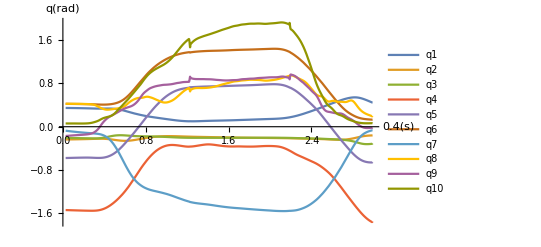

```mathematica
Plot[{qsoll[time][[1]], qsoll[time][[2]], qsoll[time][[3]], qsoll[time][[4]], qsoll[time][[5]], qsoll[time][[6]],qsoll[time][[7]], qsoll[time][[8]], qsoll[time][[9]], qsoll[time][[10]]}, {time,t0+ 0.01,tend- 0.01}, AxesLabel -> {t[s], q[rad]}, PlotLegends -> {"q1", "q2", "q3", "q4", "q5", "q6", "q7", "q8", "q9", "q10"}]
```

qua si vedono i picchi di errore che si registrano sotto

#### Hand error

```mathematica
ErrPOSsoll[time_] = ePl[time, qsoll[time]];
```

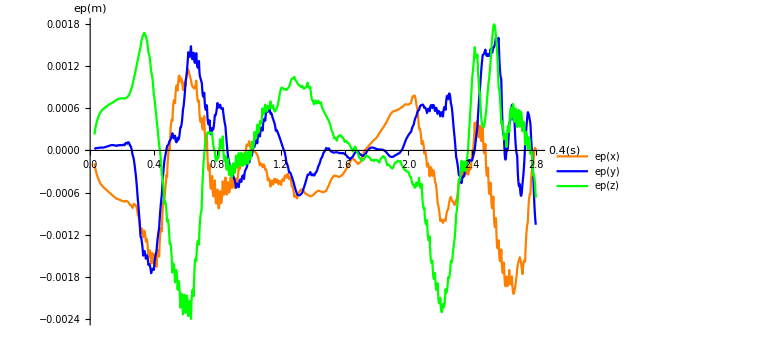

```mathematica
Plot[{ErrPOSsoll[time][[1]], ErrPOSsoll[time][[2]], ErrPOSsoll[time][[3]]}, {time, t0+0.01, tend-0.2}, PlotStyle -> {Orange, Blue, Green}, ImageSize -> Large, PlotRange -> All, TargetUnits -> { "Seconds", "Meters"}, AxesLabel -> {t[s], ep[m]}, PlotLegends -> {"ep(x)", "ep(y)", "ep(z)"}]
```

```mathematica
ErrORsoll[time_] = eOl[time, qsoll[time]];
```

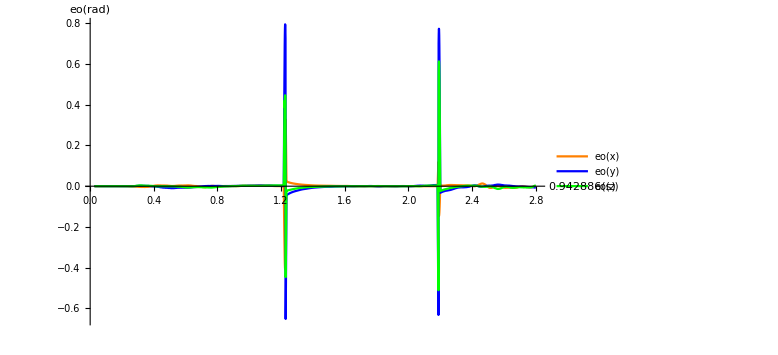

```mathematica
Plot[{ErrORsoll[time][[1]], ErrORsoll[time][[2]], ErrORsoll[time][[3]]}, {time, t0+0.01, tend-0.2}, PlotStyle -> {Orange, Blue, Green}, ImageSize -> Large, PlotRange -> All, AxesLabel -> {t[s], eo[rad]}, PlotLegends -> {"eo(x)", "eo(y)", "eo(z)"}]
```

primo picco errore

```mathematica
-Graphics-;
```

secondo picco errore

```mathematica
-Graphics-;
```

## 3D elements

### Plane

```mathematica
(* grid representing floor *)
```

```mathematica
passo = (xmax3d - xmin3d)/4; (* grid cell size, scaled in order to always hav ethe same number of cells *)
```

```mathematica
pianopts = Table[{x, y, 0}, {x, xmin3d, xmax3d, passo}, {y, ymin3d, ymax3d, passo}];
```

```mathematica
(* graphic representation of the defined grid *)
```

```mathematica
piano = Map[Graphics3D, {Map[{LightGray, Line[#]} &, pianopts], Map[{Gray, Line[#]} &, Transpose[pianopts]]}];
```

### Base

```mathematica
(* sphere representing L5 *)
```

```mathematica
rbase = 0.08;
```

```mathematica
base = Graphics3D[{Gray, Opacity[0.9], Specularity[White, 30], Sphere[L5Pos, rbase]}];
```

### Robot

```mathematica
(* Position and orientation of each joints' node of the ARM *)
```

#### Points evaluation

```mathematica
dg1l[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = RigidPosition[Tg1l[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]];
```

```mathematica
dg2l[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = RigidPosition[Tg2l[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]];
```

```mathematica
dg3l[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = RigidPosition[Tg3l[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]];
```

```mathematica
dg4l[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = RigidPosition[Tg4l[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]];
```

```mathematica
dg5l[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = RigidPosition[Tg5l[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]];
```

```mathematica
dg6l[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = RigidPosition[Tg6l[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]];
```

```mathematica
dg7l[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = RigidPosition[Tg7l[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]];
```

```mathematica
dg8l[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = RigidPosition[Tg8l[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]];
```

```mathematica
dg9l[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = RigidPosition[Tg9l[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]];
```

```mathematica
dg10l[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = RigidPosition[Tg10l[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]];
```

```mathematica
giuntil[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = {
   L5Pos,
   dg1l[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}],
   dg2l[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}],
   dg3l[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}],
   dg4l[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}],
   dg5l[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}],
   dg6l[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}],
   dg7l[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}],
   dg8l[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}],
   dg9l[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}],
   dg10l[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]   
};
```

#### Tube

```mathematica
(* Tube insertion between two consecutive joints in order to represent the link *)
```

```mathematica
rrobot = 0.05; (* human like arm dimension *)
```

```mathematica
robotl[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = Graphics3D[{Cyan, Opacity[0.6], Specularity[White, 60], CapForm["Butt"], Tube[{giuntil[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]}, rrobot]}];
```

### Reference frames

```mathematica
(* three different reference frames will be plotted: Base, Right end-effector and left end-effector *)
```

```mathematica
(* Reference frame representation, drawed using (0,0,0) as origin and (x, y, z) as axis directions. *)
```

```mathematica
lf = 0.25; (* reference frame axis length *)
e1d = {lf, 0, 0, 1}; e2d = {0, lf, 0, 1}; e3d = {0, 0, lf, 1}; Orig = {0, 0, 0, 1};
Ox = Transpose[Drop[#.Transpose[{Orig, e1d}], -1]] &;
Oy = Transpose[Drop[#.Transpose[{Orig, e2d}], -1]] &;
Oz = Transpose[Drop[#.Transpose[{Orig, e3d}], -1]] &;
Otot = {Ox[#], Oy[#], Oz[#]} &;
```

```mathematica
(* "Reference frame" representation draws over: base, right end-effector and left end-effector *)
```

```mathematica
rifg = Graphics3D[{Red, Thick, Line /@ Otot@Tg}];
```

```mathematica
rifEEl[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] :=  Graphics3D[{
{Red, Thick, Line[Ox@TgEEl[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]]},
{Green, Thick, Line[Oy@TgEEl[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]]},
{Blue, Thick, Line[Oz@TgEEl[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]]}
}];
```

```mathematica
(* x: red, y: green, z: blue *)
```

```mathematica
riftimeEEl[time_] :=  Graphics3D[{
{Red, Thick, Line [ Ox@TEEl[time]]},
{Green, Thick, Line [ Oy@TEEl[time]]},
{Blue, Thick, Line [ Oz@TEEl[time]]} }];
```

### Assiemi

```mathematica
(* Put all defined elements together *)
```

```mathematica
assiemel[{q1_,q2_,q3_,q4_,q5_, q6_, q7_, q8_, q9_, q10_}] = {base,rifg, rifEEl[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}], piano, robotl[{q1, q2, q3, q4, q5, q6, q7, q8, q9, q10}]};
```

## Animation and 3D Plots

```mathematica
Manipulate[
Show[
riftimeEEl[time],
PlotRange -> {{xmin3d, xmax3d}, {ymin3d, ymax3d}, {zmin3d, zmax3d}}, 
Boxed -> False, AxesLabel -> {"x", "y", "z"}, 
ViewPoint -> {1,1,1}],
{{time,t0, "Time"},t0,tend}]
```

```mathematica
Manipulate[Show[assiemel[{q1l, q2l, q3l, q4l, q5l, q6l, q7l, q8l, q9l, q10l}], PlotRange -> {{-1, 1.5}, {-0.5, 1}, {0, 2}}, Boxed -> False, AxesLabel -> {"x", "y", "z"}(*,ViewPoint->Right*)],
{{q1l,0},-Pi,+Pi}, {{q2l,0},-Pi,+Pi}, {{q3l,0},-Pi,+Pi}, {{q4l,0},-Pi,+Pi}, {{q5l,0},-Pi,+Pi}, {{q6l,0},-Pi,+Pi}, {{q7l,0},-Pi,+Pi}, {{q8l,0},-Pi,+Pi}, {{q9l,0},-Pi,+Pi}, {{q10l,0},-Pi,+Pi} ]
```

```mathematica
(* left hand animation of inverse kine solution and desired trajectory to be followed *)
```

```mathematica
animationl = Animate[Show[
   {assiemel [qsoll[time]]},
   {ParametricPlot3D[posl[k], {k, t0, time},
     			PlotPoints -> 500,
     			MaxRecursion -> 13
     			]} (* Desired Trajectory *),
   PlotRange -> {{xmin3d, xmax3d}, {ymin3d, ymax3d}, {zmin3d, zmax3d}}, Boxed -> False, AxesLabel -> {"x", "y", "z"}, ViewPoint -> {1,1,0.5}], {time, t0 + 0.01, tend - 0.01, 0.0001}]
```

## Both arms

## 3D elements

```mathematica
assiemeboth[{q1r_, q2r_,q3r_, q4r_, q5r_, q6r_, q7r_, q8r_, q9r_, q10r_}, {q1l_, q2l_,q3l_, q4l_, q5l_, q6l_, q7l_, q8l_, q9l_, q10l_}] = 
{base,
rifg, 
rifEEr[{q1r, q2r,q3r, q4r, q5r, q6r, q7r, q8r, q9r, q10r}], 
rifEEl[{q1l, q2l,q3l, q4l, q5l, q6l, q7l, q8l, q9l, q10l}], 
piano, 
robotr[{q1r, q2r,q3r, q4r, q5r, q6r, q7r, q8r, q9r, q10r}],
robotl[{q1l, q2l,q3l, q4l, q5l, q6l, q7l, q8l, q9l, q10l}]
};
```

## Animation

```mathematica
(* left and right hands animation of inverse kine solution and desired trajectory to be followed *)
```

```mathematica
Manipulate[
Show[
{riftimeEEl[time],riftimeEEr[time]},
PlotRange -> {{xmin3d, xmax3d}, {ymin3d, ymax3d}, {zmin3d, zmax3d}}, 
Boxed -> False, AxesLabel -> {"x", "y", "z"}, 
ViewPoint -> {1,1,1}],
{{time,t0, "Time"},t0,tend}]
```

```mathematica
animationboth = Animate[Show[
       {assiemer [qsolr[time]]},
{assiemel [qsoll[time]]},
   {ParametricPlot3D[posr[k], {k, t0, time},
     			PlotPoints -> 500,
     			MaxRecursion -> 13
     			]} (* Desired Trajectory *),
{ParametricPlot3D[posl[k], {k, t0, time},
     			PlotPoints -> 500,
     			MaxRecursion -> 13
     			]} (* Desired Trajectory *),
   PlotRange -> {{xmin3d, xmax3d}, {ymin3d, ymax3d}, {zmin3d, zmax3d}}, Boxed -> False, AxesLabel -> {"x", "y", "z"}, ViewPoint -> {1,1,0.5}], {time, t0 + 0.01, tend - 0.01, 0.0001}]
```

```mathematica
(* both arms *)
```

```mathematica
Manipulate[Show[assiemeboth[{q1r, q2r,q3r, q4r, q5r, q6r, q7r, q8r, q9r, q10r},{q1l, q2l,q3l, q4l, q5l, q6l, q7l, q8l, q9l, q10l}], PlotRange -> {{xmin3d, xmax3d}, {ymin3d, ymax3d}, {zmin3d, zmax3d}}, Boxed -> False, AxesLabel -> {"x", "y", "z"}, ViewPoint -> {2,2,2}],{{q1r,0},-Pi,+Pi}, {{q2r,0},-Pi,+Pi}, {{q3r,0},-Pi,+Pi}, {{q4r,0},-Pi,+Pi}, {{q5r,0},-Pi,+Pi}, {{q6r,0},-Pi,+Pi}, {{q7r,0},-Pi,+Pi}, {{q8r,0},-Pi,+Pi}, {{q9r,0},-Pi,+Pi}, {{q10r,0},-Pi,+Pi},{{q1l,0},-Pi,+Pi}, {{q2l,0},-Pi,+Pi}, {{q3l,0},-Pi,+Pi}, {{q4l,0},-Pi,+Pi}, {{q5l,0},-Pi,+Pi}, {{q6l,0},-Pi,+Pi}, {{q7l,0},-Pi,+Pi}, {{q8l,0},-Pi,+Pi}, {{q9l,0},-Pi,+Pi}, {{q10l,0},-Pi,+Pi}  ];
```